# Rolling down. Automatic Image Processing

#### Import the picture (do picture on a monotone background)

```mathematica
image =Import[FileNameJoin[{NotebookDirectory[],"track1.jpg"}]];
p1 = Show[image,ImageSize -> 400,  PlotLabel -> "Original photo"]
```

-Graphics-

#### Crop to make yellow shape hit the border on both sides

```mathematica
image = ImageCrop[image, {2500, 1000}];
Show[image,ImageSize -> 400 ]
```

-Graphics-

#### Detect edge

```mathematica
Edges = EdgeDetect[image];
p2 = Show[Edges,ImageSize -> 400,  PlotLabel -> "Edges"]
```

-Graphics-

#### Extract top line

```mathematica
EdgesSeparated = MorphologicalComponents[Edges];
TopEdge = Replace[EdgesSeparated,n_?(#==2&)->0, All]; 
Show[Image[TopEdge], ImageSize->400]
```

-Graphics-

#### Convert to coordinates

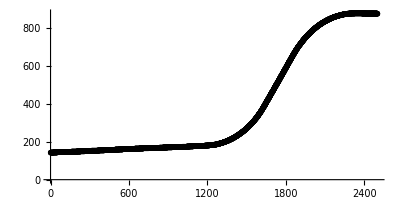

```mathematica
pst =PixelValuePositions[Image[TopEdge],1];
p3 =ListPlot[pst, AspectRatio->Automatic, ImageSize->400,  PlotLabel -> "Coordinates of top line"]
```

#### Remove duplicates in x and do interpolation

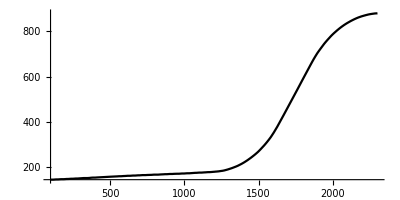

```mathematica
AA1=Union[pst,SameTest->(#1[[1]]==#2[[1]]&)];
smothed = MovingAverage[AA1, 20];
ff= Interpolation[smothed];
p4 =Plot[ff[x], {x, 100, 2300}, AspectRatio->Automatic, ImageSize->400,  PlotLabel -> "Interpolation"]
```

#### Get derivative

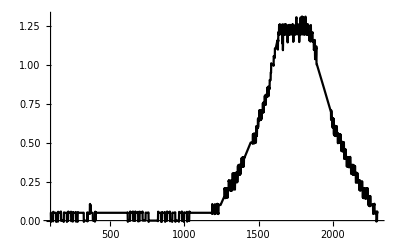

```mathematica
Plot[ff'[x], {x, 100, 2300}, ImageSize->400]
```